```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t]
```

```mathematica
β[0,0,t,-ϵ,9]//MatrixForm
```

(ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t
t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | 0 | 0
0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0 | 0
0 | 0 | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ | t
t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ϵ)

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[1,0.0001,0.5,0,9]
```

3.

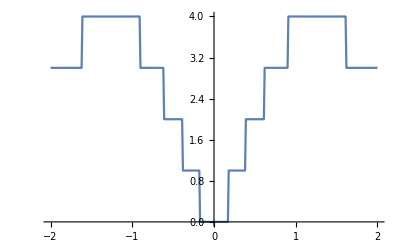
{22.583,-Graphics-}

```mathematica
Timing[ListLinePlot[ParallelTable[{ω,Abs[tr[ω,0.0001,1,0,9]]},{ω,Range[-2,2,0.01]}]]]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/9AGNR/leads/sl"<>ToString[x]<>".dat",SL[x,0.0001,1,0,9]],{x,-2,2,0.01}]
```

```mathematica
Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/9AGNR/leads/sl"<>ToString[x]<>".dat"]],{x,-2,2,0.01}]
```

{1}
 |  |  |  |

```mathematica
m[ω_,δ_,t_,ϵ_,m_,ϵ1_]:=Module[{Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,2m}], μ2=RandomInteger[{1,2m}], μ3=RandomInteger[{1,2m}], μ4=RandomInteger[{1,2m}],μ5=RandomInteger[{1,2m}], μ6=RandomInteger[{1,2m}], μ7=RandomInteger[{1,2m}],μ8=RandomInteger[{1,2m}], μ9=RandomInteger[{1,2m}], μ10=RandomInteger[{1,2m}], μ11=RandomInteger[{1,2m}],μ12=RandomInteger[{1,2m}], μ13=RandomInteger[{1,2m}], μ14=RandomInteger[{1,2m}](*, μ15=RandomInteger[{8,42}],μ16=RandomInteger[{8,42}]*),J=LEFT[ω,δ,t,ϵ,m]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp4,imp11,imp4,imp,imp,imp3,imp13,imp11,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp4,imp8,imp1,imp2,imp,imp10,imp,imp14,imp4,imp,imp10,imp10,imp,imp,imp1,imp,imp,imp3,imp9,imp,imp,imp2,imp,imp,imp12,imp,imp11,imp,imp,imp5,imp,imp7,imp8,imp,imp2,imp4,imp6,imp,imp,imp9,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp6,imp7,imp,imp,imp5,imp,imp,imp8,imp13,imp,imp,imp,imp9,imp,imp6,imp,imp,imp12,imp,imp14,imp,imp14,imp,imp13,imp3,imp,imp,imp,imp,imp1,imp5,imp,imp,imp,imp12,imp}]};
sl1= Module[{},Do[J=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];
 J=J];
Il1:=Inverse[IdentityMatrix[2m]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Mean[Table[m[1,0.0001,1,0,9,0.5],2000]]//AbsoluteTime
```

$Aborted

```mathematica
Mean[ParallelTable[Cfun[1],2000]]//Timing
```

{1.37154,2.20026}

```mathematica
Table[{ω,Mean[ParallelTable[Cfun[ω],2000]]},{ω,-2,2,0.01}]
```

{{-2.,1.28278},{-1.99,1.34144},{-1.98,1.37295},{-1.97,1.3888},{-1.96,1.42696},{-1.95,1.4383},{-1.94,1.44839},{-1.93,1.46295},{-1.92,1.50769},{-1.91,1.49369},{-1.9,1.46402},{-1.89,1.4318},{-1.88,1.5142},{-1.87,1.52503},{-1.86,1.56951},{-1.85,1.56828},{-1.84,1.57311},{-1.83,1.62324},{-1.82,1.60008},{-1.81,1.62119},{-1.8,1.63009},{-1.79,1.53152},{-1.78,1.58177},{-1.77,1.64629},{-1.76,1.67114},{-1.75,1.706},{-1.74,1.69179},{-1.73,1.72255},{-1.72,1.75239},{-1.71,1.75235},{-1.7,1.6642},{-1.69,1.61006},{-1.68,1.76439},{-1.67,1.79559},{-1.66,1.83708},{-1.65,1.86615},{-1.64,1.90186},{-1.63,1.95801},{-1.62,2.05537},{-1.61,1.38247},{-1.6,1.14651},{-1.59,1.17591},{-1.58,1.22254},{-1.57,1.259},{-1.56,1.31806},{-1.55,1.33312},{-1.54,1.34714},{-1.53,1.3359},{-1.52,1.40834},{-1.51,1.43704},{-1.5,1.47345},{-1.49,1.50916},{-1.48,1.50785},{-1.47,1.48944},{-1.46,1.48911},{-1.45,1.53373},{-1.44,1.5694},{-1.43,1.58832},{-1.42,1.61235},{-1.41,1.57587},{-1.4,1.52991},{-1.39,1.61982},{-1.38,1.60572},{-1.37,1.66865},{-1.36,1.68949},{-1.35,1.67135},{-1.34,1.70559},{-1.33,1.71711},{-1.32,1.74232},{-1.31,1.71854},{-1.3,1.6556},{-1.29,1.70559},{-1.28,1.73617},{-1.27,1.77019},{-1.26,1.76728},{-1.25,1.78532},{-1.24,1.78851},{-1.23,1.82634},{-1.22,1.8314},{-1.21,1.81267},{-1.2,1.82111},{-1.19,1.84349},{-1.18,1.86149},{-1.17,1.83157},{-1.16,1.82942},{-1.15,1.85011},{-1.14,1.87013},{-1.13,1.88916},{-1.12,1.90345},{-1.11,1.90601},{-1.1,1.92571},{-1.09,1.95119},{-1.08,1.95019},{-1.07,1.99101},{-1.06,2.00102},{-1.05,2.04322},{-1.04,2.07585},{-1.03,2.08846},{-1.02,2.12866},{-1.01,2.1332},{-1.,2.15234},{-0.99,2.16818},{-0.98,1.82755},{-0.97,1.19121},{-0.96,0.530956},{-0.95,0.33973},{-0.94,0.42931},{-0.93,0.541793},{-0.92,0.661888},{-0.91,0.69016},{-0.9,0.655425},{-0.89,0.579981},{-0.88,0.586112},{-0.87,0.727389},{-0.86,0.854299},{-0.85,0.964268},{-0.84,1.00873},{-0.83,1.04906},{-0.82,1.07865},{-0.81,1.10119},{-0.8,1.1144},{-0.79,1.14781},{-0.78,1.17235},{-0.77,1.16058},{-0.76,1.15631},{-0.75,1.16131},{-0.74,1.16788},{-0.73,1.17014},{-0.72,1.1585},{-0.71,1.15388},{-0.7,1.13941},{-0.69,1.11554},{-0.68,1.13302},{-0.67,1.09331},{-0.66,1.06444},{-0.65,1.03985},{-0.64,0.974731},{-0.63,0.919507},{-0.62,0.800838},{-0.61,0.616414},{-0.6,0.560493},{-0.59,0.741935},{-0.58,0.847292},{-0.57,0.869667},{-0.56,0.884072},{-0.55,0.904736},{-0.54,0.914455},{-0.53,0.912505},{-0.52,0.915837},{-0.51,0.905081},{-0.5,0.907567},{-0.49,0.864712},{-0.48,0.868753},{-0.47,0.845987},{-0.46,0.834976},{-0.45,0.843495},{-0.44,0.822819},{-0.43,0.774657},{-0.42,0.769085},{-0.41,0.724382},{-0.4,0.669223},{-0.39,0.592645},{-0.38,0.438078},{-0.37,0.331525},{-0.36,0.391727},{-0.35,0.581366},{-0.34,0.659757},{-0.33,0.677976},{-0.32,0.676596},{-0.31,0.700296},{-0.3,0.691772},{-0.29,0.694934},{-0.28,0.69216},{-0.27,0.687382},{-0.26,0.702894},{-0.25,0.676008},{-0.24,0.683134},{-0.23,0.654868},{-0.22,0.642348},{-0.21,0.624913},{-0.2,0.589442},{-0.19,0.532174},{-0.18,0.42937},{-0.17,0.0000824991},{-0.16,0.0000111511},{-0.15,4.41743×10^-6},{-0.14,2.46089×10^-6},{-0.13,1.62723×10^-6},{-0.12,1.19349×10^-6},{-0.11,9.38337×10^-7},{-0.1,7.75354×10^-7},{-0.09,6.65062×10^-7},{-0.08,5.8731×10^-7},{-0.07,5.3093×10^-7},{-0.06,4.89339×10^-7},{-0.05,4.58469×10^-7},{-0.04,4.35721×10^-7},{-0.03,4.19402×10^-7},{-0.02,4.08416×10^-7},{-0.01,4.02074×10^-7},{0.,3.99994×10^-7},{0.01,4.01502×10^-7},{0.02,4.05246×10^-7},{0.03,4.11622×10^-7},{0.04,4.21846×10^-7},{0.05,4.37273×10^-7},{0.06,4.59145×10^-7},{0.07,4.91766×10^-7},{0.08,5.30039×10^-7},{0.09,5.86763×10^-7},{0.1,6.64154×10^-7},{0.11,7.69547×10^-7},{0.12,9.38385×10^-7},{0.13,1.17936×10^-6},{0.14,1.60893×10^-6},{0.15,2.47096×10^-6},{0.16,4.47256×10^-6},{0.17,0.0000128999},{0.18,0.00264191},{0.19,0.241523},{0.2,0.467691},{0.21,0.57615},{0.22,0.631611},{0.23,0.663198},{0.24,0.686979},{0.25,0.71738},{0.26,0.733585},{0.27,0.746379},{0.28,0.750813},{0.29,0.761127},{0.3,0.768642},{0.31,0.766763},{0.32,0.784856},{0.33,0.797446},{0.34,0.791032},{0.35,0.803924},{0.36,0.802577},{0.37,0.809422},{0.38,0.820298},{0.39,0.648431},{0.4,0.631446},{0.41,0.728256},{0.42,0.799512},{0.43,0.891638},{0.44,0.926315},{0.45,0.956499},{0.46,0.994266},{0.47,1.02031},{0.48,1.04622},{0.49,1.07318},{0.5,1.08479},{0.51,1.11089},{0.52,1.11346},{0.53,1.14054},{0.54,1.13256},{0.55,1.14317},{0.56,1.16206},{0.57,1.16108},{0.58,1.18398},{0.59,1.20024},{0.6,1.19706},{0.61,1.24026},{0.62,1.25565},{0.63,0.907478},{0.64,0.998686},{0.65,1.1276},{0.66,1.19714},{0.67,1.23942},{0.68,1.29812},{0.69,1.34329},{0.7,1.3746},{0.71,1.42435},{0.72,1.42007},{0.73,1.43895},{0.74,1.46697},{0.75,1.50373},{0.76,1.53098},{0.77,1.55122},{0.78,1.57151},{0.79,1.56063},{0.8,1.59162},{0.81,1.62162},{0.82,1.63842},{0.83,1.65587},{0.84,1.67289},{0.85,1.67739},{0.86,1.70384},{0.87,1.74911},{0.88,1.76413},{0.89,1.80699},{0.9,1.85987},{0.91,1.47753},{0.92,1.452},{0.93,1.56486},{0.94,1.6725},{0.95,1.77641},{0.96,1.86281},{0.97,1.94256},{0.98,2.02593},{0.99,2.10876},{1.,2.18101},{1.01,2.22151},{1.02,1.93439},{1.03,1.30273},{1.04,0.618424},{1.05,0.351659},{1.06,0.389547},{1.07,0.535369},{1.08,0.712},{1.09,0.835932},{1.1,0.949609},{1.11,1.0457},{1.12,1.09858},{1.13,1.16684},{1.14,1.19771},{1.15,1.25681},{1.16,1.28914},{1.17,1.29829},{1.18,1.32774},{1.19,1.32127},{1.2,1.33714},{1.21,1.36214},{1.22,1.37063},{1.23,1.40364},{1.24,1.39959},{1.25,1.40462},{1.26,1.42766},{1.27,1.43528},{1.28,1.42015},{1.29,1.43907},{1.3,1.44555},{1.31,1.44167},{1.32,1.40291},{1.33,1.35474},{1.34,1.39804},{1.35,1.41809},{1.36,1.41429},{1.37,1.4132},{1.38,1.41111},{1.39,1.3919},{1.4,1.38727},{1.41,1.37506},{1.42,1.35069},{1.43,1.30153},{1.44,1.32815},{1.45,1.3434},{1.46,1.3204},{1.47,1.32789},{1.48,1.30683},{1.49,1.25801},{1.5,1.25595},{1.51,1.24808},{1.52,1.24648},{1.53,1.22807},{1.54,1.20401},{1.55,1.14079},{1.56,1.10332},{1.57,1.10532},{1.58,1.08619},{1.59,1.02906},{1.6,0.968522},{1.61,0.875287},{1.62,0.690042},{1.63,0.498228},{1.64,0.494883},{1.65,0.611013},{1.66,0.74892},{1.67,0.887048},{1.68,0.983129},{1.69,1.04079},{1.7,1.09519},{1.71,1.06415},{1.72,1.00053},{1.73,1.11158},{1.74,1.12608},{1.75,1.15499},{1.76,1.16817},{1.77,1.17973},{1.78,1.16531},{1.79,1.18376},{1.8,1.1653},{1.81,1.06191},{1.82,1.08774},{1.83,1.14128},{1.84,1.13776},{1.85,1.14931},{1.86,1.14344},{1.87,1.15524},{1.88,1.14378},{1.89,1.13823},{1.9,1.11759},{1.91,1.06004},{1.92,1.06527},{1.93,1.08856},{1.94,1.08917},{1.95,1.06699},{1.96,1.07033},{1.97,1.08162},{1.98,1.07074},{1.99,1.05811},{2.,1.03955}}

```mathematica
Cfun= Compile[{ω},m[ω,0.0001,1,0,9,0.5],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Cfun[1]
```

2.33915

```mathematica
CompilePrint[Cfun]
```

CompilePrint[CompiledFunction[…]]

```mathematica
Needs["CompiledFunctionTools`"]
```

CompilePrint::shdw: Symbol CompilePrint appears in multiple contexts {CompiledFunctionTools`,Global`}; definitions in context CompiledFunctionTools` may shadow or be shadowed by other definitions.